## Tools

```mathematica
ModTikZ[m_]:="{"<>ToString[m["ParameterTable"][[1,1]][[3,2]]]<>"*x+"<>ToString[m["ParameterTable"][[1,1]][[2,2]]]<>"};"
ToTikz[a_]:="("<>ToString@CForm[a[[1]]]<>","<>ToString@CForm[a[[2]]]<>")\n";
ToTikz2[a_]:="{"<>(ToTikz/@a//StringJoin)<>"};";
SubTable[table_,columns_,line_]:=Select[table,#[[columns]]==line&] [[ All,Complement[Range[1,Length[table[[1]] ] ],columns ] ]]//Transpose;
TableReduce[table_,columns_,f_]:=
Module[{reduced},
reduced=Union@table[[All,columns]];
Table[Join[reduced[[k]],f/@SubTable[table,columns,reduced[[k]] ] ],{k,Length[reduced]}]
];
ViewTable[table_,title_,columns_]:=Join[{Range[1,Length[title]],title},table][[All,columns]]//N//TableForm[#]&;
TableTitle[title_]:=Column[Table[{k,title[[1,k]]},{k,1,Length@title[[1]]}]];
```

```mathematica
title = ReadList["/home/vadym/projects/builds/sqct-gc-debug/out/uniform.txt.title"];
```

```mathematica
TableTitle[title]
```

{1,Angle string}
{2,Angle value}
{3,T count}
{4,Precision}
{5,{{x[0],x[1],x[2],x[3]},{y[0],y[1],y[2],y[3]},m,k,Solutions}}
{6,Matrix product}
{7,T-count}
{8,H-count}
{9,Phase-count}
{10,Pauli-X-count}
{11,Pauli-Y-count}
{12,Pauli-Z-count}
{13,n}
{14,phi}
{15,delta}
{16,find_halves_real_time}
{17,find_halves_cpu_time}
{18,merge_halves_time}
{19,tcount_time}
{20,halves_size}
{21,b_max}
{22,max_tuples_memory_size}
{23,tuples_processed}
{24,factor_calls}
{25,norm_equation_calls}

```mathematica
tableU = ReadList["/home/vadym/projects/builds/sqct-gc-debug/out/uniform.txt"];
summary=TableReduce[tableU[[All,{3,4,16,20}]],{1},N[Mean[#],20]&][[8;;All]];
```

```mathematica
summary//TableForm
```

7 | 0.0446252 | 0. | 0
8 | 0.0422779 | 1.9007375190000000042 | 135.972
9 | 0.0357748 | 1.4424194199999999914 | 128.34
10 | 0.0288655 | 1.2990229669999999856 | 208.28
11 | 0.025004 | 1.2719469219999999957 | 159.768
12 | 0.023858 | 1.2461158409999999933 | 286.293
13 | 0.0192549 | 1.1902672540000000118 | 270.109
14 | 0.015787 | 1.4520152999999999985 | 431.41
15 | 0.013419 | 1.2433582179999999998 | 342.05
16 | 0.0101043 | 1.5946235360000000016 | 607.056
17 | 0.00812107 | 1.4210358949999999999 | 423.46
18 | 0.00662353 | 1.673687486000000001 | 731.641
19 | 0.00533614 | 1.5072204129999999996 | 552.533
20 | 0.00374706 | 1.6599933020000000023 | 920.783
21 | 0.00304283 | 1.3904997559999999837 | 526.719
22 | 0.00227667 | 1.8195417700000000106 | 946.688
23 | 0.00162161 | 1.4935955719999999922 | 602.78
24 | 0.00136866 | 1.5986565259999999801 | 894.018
25 | 0.00118617 | 1.485195844000000003 | 645.922
26 | 0.000986373 | 1.9161682279999999937 | 1277.006
27 | 0.000824531 | 1.8145096690000000137 | 852.454
28 | 0.000635958 | 2.524898773999999993 | 1690.447
29 | 0.000494463 | 1.8280541500000000051 | 1021.439
30 | 0.000407489 | 2.2477317990000000056 | 1827.1
31 | 0.000335073 | 2.1102542739999999953 | 1223.424
32 | 0.000276167 | 2.531658130999999987 | 2190.163
33 | 0.000223006 | 2.1720294839999999991 | 1572.311
34 | 0.000181795 | 2.9527153949999999816 | 2948.083
35 | 0.000141323 | 2.5353640090000000042 | 2121.559
36 | 0.000118248 | 2.8930555510000000132 | 3431.09
37 | 0.0000990756 | 2.7197460719999999998 | 2889.022
38 | 0.0000792818 | 3.4117073400000000173 | 4754.417
39 | 0.000059921 | 3.2339928189999999926 | 3517.865
40 | 0.0000494193 | 3.2641312519999999981 | 5092.382
41 | 0.0000401728 | 3.2219588130000000147 | 4092.55
42 | 0.0000318431 | 4.4758501540000000171 | 7197.012
43 | 0.0000259453 | 3.7616387410000000024 | 5480.052
44 | 0.0000216375 | 4.474234320000000013 | 9574.024
45 | 0.0000173319 | 4.344459375999999957 | 7925.596
46 | 0.0000135201 | 5.3171213050000000314 | 12378.
47 | 0.0000106565 | 4.3494598029999999773 | 8995.388
48 | 8.06514×10^-6 | 5.4017958089999999717 | 14153.244
49 | 6.36419×10^-6 | 4.8625888990000000358 | 10769.708
50 | 5.01206×10^-6 | 5.6397038269999999862 | 16957.831
51 | 4.01737×10^-6 | 5.1317744589999999847 | 13426.943
52 | 3.26802×10^-6 | 7.1260509089999999945 | 22373.126
53 | 2.77151×10^-6 | 5.7390836410000000056 | 17546.61
54 | 2.20998×10^-6 | 8.2905468670000000002 | 29626.727
55 | 1.64021×10^-6 | 7.4082972110000000061 | 23761.195
56 | 1.30496×10^-6 | 9.5982438170000000095 | 35222.822
57 | 1.05228×10^-6 | 8.9263877370000000417 | 28219.046
58 | 8.14929×10^-7 | 12.130786606999999971 | 45320.135
59 | 6.47782×10^-7 | 10.276529961999999965 | 35403.167
60 | 5.33038×10^-7 | 14.706063382999999968 | 56045.624
61 | 4.10291×10^-7 | 13.633575484000000024 | 46457.244
62 | 3.26117×10^-7 | 19.061166852999999969 | 71278.807
63 | 2.70105×10^-7 | 16.427414757999999929 | 57211.171
64 | 2.13679×10^-7 | 25.122088859000000048 | 94113.676
65 | 1.64038×10^-7 | 21.935153778999999989 | 75252.876
66 | 1.25947×10^-7 | 31.950628994999999973 | 115076.443
67 | 1.02974×10^-7 | 27.924958616999999768 | 89612.843
68 | 8.062×10^-8 | 41.359429577000000091 | 145337.449
69 | 6.60203×10^-8 | 36.096857668000000094 | 115449.809
70 | 5.14289×10^-8 | 53.335213752000000021 | 187372.795
71 | 4.11504×10^-8 | 46.616263322999999925 | 148354.879
72 | 3.36862×10^-8 | 69.107798225000000301 | 235393.959
73 | 2.66964×10^-8 | 62.613770762000000126 | 195475.019
74 | 2.13114×10^-8 | 91.591392499999999806 | 307212.842
75 | 1.74755×10^-8 | 82.615808673999999868 | 249614.038
76 | 1.44336×10^-8 | 123.71278776300000034 | 404477.419
77 | 1.14276×10^-8 | 112.0206553320000002 | 339404.787
78 | 8.80693×10^-9 | 168.47674752399999963 | 532251.299
79 | 6.95664×10^-9 | 149.31139151900000049 | 420129.631
80 | 5.90808×10^-9 | 223.49855973299999941 | 656549.025
81 | 4.54976×10^-9 | 209.10325825599999911 | 566825.329
82 | 3.57651×10^-9 | 306.75314840299999943 | 865295.787
83 | 2.84754×10^-9 | 277.06481037100000032 | 698735.975
84 | 2.19213×10^-9 | 417.18092144000000059 | 1.097198411×10^6
85 | 1.78286×10^-9 | 375.26059038400000131 | 872866.531
86 | 1.44957×10^-9 | 563.33788413500000064 | 1.393778393×10^6
87 | 1.11724×10^-9 | 520.24042484799999909 | 1.165620609×10^6
88 | 8.37902×10^-10 | 766.42192762200000129 | 1.774732461×10^6
89 | 6.84574×10^-10 | 694.49931267400000127 | 1.392283221×10^6

```mathematica
precision={Log2[1/#[[2]]],#[[1]]}&/@summary[[All,{1,2}]];
mpr=LinearModelFit[precision,x,x];
ModTikZ@mpr
```

{3.10269*x+-4.86078};

{0.214792542791383782274*x+-9.5314702302301138772};

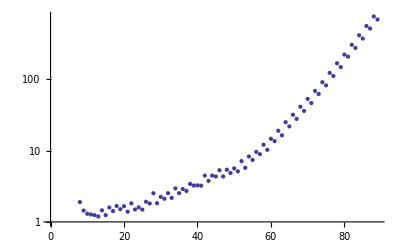

```mathematica
time={#[[1]],Log2[#[[2]]]}&/@summary[[66;;All,{1,3}]];
mt=LinearModelFit[time,x,x];
ModTikZ@mt
Time[nT_]:=2^(nT*0.211327639389661897797-9.0604346582257450628);
ListLogPlot[summary[[All,{1,3}]]]
```

{0.15660715866027550130*x+-5.0971171416574815211};

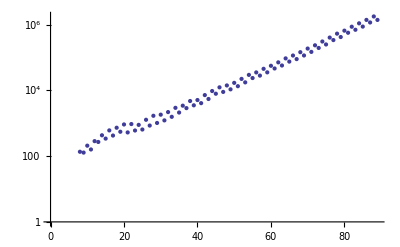

```mathematica
memory={#[[1]],Log2[#[[2]]]}&/@summary[[30;;All,{1,3}]];
mmt=LinearModelFit[memory,x,x];
ModTikZ@mmt
Memory[nT_]:=2^(nT*0.134640178405898530238-3.1865905313076279607) * 16/2^30;
ListLogPlot[summary[[All,{1,4}]]]
```

```mathematica
Table[{n,Memory[n]},{n,150,200}]//TableForm
```

150 | 0.00196594166599688832
151 | 0.00215824806143436808
152 | 0.00236936567104254076
153 | 0.0026011345884790857
154 | 0.00285557490347414769
155 | 0.00313490430886135297
156 | 0.00344155742991052285
157 | 0.00377820704443586913
158 | 0.00414778737863338744
159 | 0.00455351968169314784
160 | 0.00499894030209390364
161 | 0.00548793151029201419
162 | 0.00602475533645415424
163 | 0.00661409071816229735
164 | 0.00726107428186906321
165 | 0.00797134511355315883
166 | 0.00875109390879437126
167 | 0.00960711693065843628
168 | 0.0105468752456868092
169 | 0.0115785597542901403
170 | 0.0127111625823480775
171 | 0.0139545554562620661
172 | 0.0153195757445753517
173 | 0.016818120916095916
174 | 0.0184632522378160232
175 | 0.0202693086164557957
176 | 0.0222520315758697061
177 | 0.0244287024596146659
178 | 0.0268182930545324644
179 | 0.0294416309481764052
180 | 0.0323215810613316525
181 | 0.0354832449378603467
182 | 0.03895417952887477
183 | 0.0427646373781537156
184 | 0.0469478303022497007
185 | 0.0515402188635135605
186 | 0.0565818301590731206
187 | 0.0621166066956035061
188 | 0.0681927893906693106
189 | 0.0748633380388648482
190 | 0.0821863929075205749
191 | 0.0902257814852276151
192 | 0.0990515747999827051
193 | 0.108740698155802932
194 | 0.119377601610969116
195 | 0.131054996041762609
196 | 0.143874661207201163
197 | 0.157948332857837641
198 | 0.173398676620630691
199 | 0.19036035714823362
200 | 0.208981211851369065

```mathematica
Table[{n,Sum[Time[j],{j,n}]/10^3/60/60/24/3},{n,100,200}]//TableForm
```

100 | 0.000121937155062023892
101 | 0.000141173129540876123
102 | 0.000163443638924487242
103 | 0.000189227390548340754
104 | 0.000219078609321531306
105 | 0.000253638950859280937
106 | 0.000293651293949225774
107 | 0.000339975708822230624
108 | 0.000393607944467674588
109 | 0.000455700832380321207
110 | 0.000527589066814941909
111 | 0.000610817894203310526
112 | 0.000707176328416112135
113 | 0.000818735605835901954
114 | 0.000947893706837632377
115 | 0.00109742690067144223
116 | 0.00127054942171129688
117 | 0.00147098255981777598
118 | 0.00170303464992084563
119 | 0.00197169368020852483
120 | 0.00228273450954583981
121 | 0.00264284299877566017
122 | 0.00305975972411897962
123 | 0.00354244636181183791
124 | 0.00410127832043709759
125 | 0.00474826776160671494
126 | 0.00549732180285147221
127 | 0.00636454145282101016
128 | 0.00736856770444301457
129 | 0.00853098222535653634
130 | 0.00987677125850954065
131 | 0.0114348627045210269
132 | 0.0132387479304590821
133 | 0.0153272016708909516
134 | 0.0177451154955666484
135 | 0.0205444627592263659
136 | 0.023785415775246364
137 | 0.0275376392269081075
138 | 0.0318817876183248047
139 | 0.036911238952916997
140 | 0.0427341019050690413
141 | 0.0494755396293678552
142 | 0.057280460157989027
143 | 0.0663166312166526636
144 | 0.0767782864125006518
145 | 0.08889030030934683
146 | 0.102913022134055548
147 | 0.119147872015161119
148 | 0.137943820045564873
149 | 0.159704887437558545
150 | 0.184898831008422849
151 | 0.214067197670686225
152 | 0.247836965049547195
153 | 0.286934018443962091
154 | 0.33219875382033255
155 | 0.384604142227059203
156 | 0.445276643926771861
157 | 0.515520421798078121
158 | 0.596845374476875987
159 | 0.690999591813047323
160 | 0.800006930276561425
161 | 0.926210516000959654
162 | 1.07232311056748585
163 | 1.24148542214858064
164 | 1.43733361541593353
165 | 1.66407747134686092
166 | 1.92659087698365146
167 | 2.23051659023437378
168 | 2.58238753164741209
169 | 2.9897672103413259
170 | 3.46141230256264963
171 | 4.00746087751770746
172 | 4.63965031641582468
173 | 5.37156960892054431
174 | 6.21895145015206629
175 | 7.20001041690186553
176 | 8.33583449219877227
177 | 9.65083835409516758
178 | 11.1732881721714469
179 | 12.9359091923240949
180 | 14.9765891699470419
181 | 17.3391927718889641
182 | 20.0745044528566606
183 | 23.2413200735086466
184 | 26.9077107247040048
185 | 31.1524859239640075
186 | 36.0668876357342265
187 | 41.7565515286208023
188 | 48.3437776270661394
189 | 55.9701591654007787
190 | 64.7996261518122919
191 | 75.0219690640126559
192 | 86.8569184188754208
193 | 100.558867906893261
194 | 116.422342615811386
195 | 134.788329883575669
196 | 156.051608863057458
197 | 180.669236348449381
198 | 209.170371267213139
199 | 242.167649016240807
200 | 280.37035013498293

```mathematica
0.0000000000000004
```

4.×10^-16